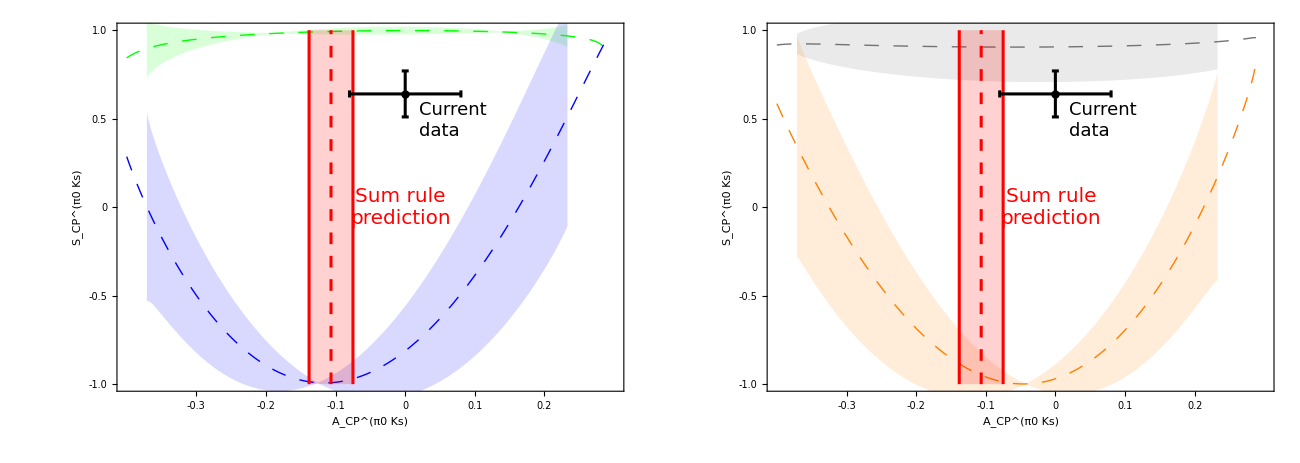

```mathematica
ClearAll["Global`*"];

SetDirectory[NotebookDirectory[]];

Get["inputs.wl"];
Get["parameters.wl"];

(*--------Calculate phi00--------*)
ClearAll[phi00sol];
phi00sol[A_?NumericQ]:=Module[
{A00,Amp,A32,A00bar,Ampbar,A32bar,phi32,phi1,phi2,phi001,phi002,phi003,phi004},

A00=Sqrt[2*BrB0pi0K00 (1-A)];
Amp=Sqrt[BrB0pimKp0 (1-AcppimKp0)];
A32=RTC0*Vus0/Vud0*Sqrt[2*BrBppippi00] (Exp[I gamma0]-q0 Exp[I phi0]);
A00bar=Sqrt[2*BrB0pi0K00 (1+A)];
Ampbar=Sqrt[BrB0pimKp0 (1+AcppimKp0)];
A32bar=RTC0*Vus0/Vud0*Sqrt[2*BrBppippi00] (Exp[-I gamma0]-q0 Exp[-I phi0]);
phi32=Arg[A32]/Degree;
phi1=ArcCos[(Abs[A00]^2+Abs[A32]^2-Abs[Amp]^2)/(2 Abs[A00] Abs[A32])]/Degree;
phi2=ArcCos[(Abs[A00bar]^2+Abs[A32bar]^2-Abs[Ampbar]^2)/(2 Abs[A00bar] Abs[A32bar])]/Degree;
phi001=phi1+phi2-2 phi32;
phi002=360-(phi2+2 phi32-phi1);
phi003=360-phi1-phi2-2 phi32;
phi004=360-(2 phi32-phi2+phi1);

{phi001,phi002,phi003,phi004}
];

(*--------Calculate Scp^{pi0Ks}--------*)
ClearAll[ScpBranch];
ScpBranch[A_?NumericQ,k_Integer]:=Module[{phi00k},phi00k=phi00sol[A][[k]];
Sqrt[1-A^2]*Sin[phid0-phi00k Degree]];

(*-------Coordinate axis definition--------*)
Amin=-0.4;Amax=0.30;
ymin=-1.0;ymax=1.0;

xMajor=Range[-0.3,0.2,0.1];
xMinor=Range[Amin,Amax,0.02];

yMajor=Range[-1,1,0.5];
yMinor=Range[ymin,ymax,0.1];

mkFrameTicks[major_,minor_,labfmt_,majLen_,minLen_]:=Module[{minorOnly,clean},clean[x_]:=Chop[x,10^-10];
minorOnly=Complement[minor,major];
Join[({clean[#],labfmt[clean[#]],{majLen,0}}&/@major),({clean[#],"",{minLen,0}}&/@minorOnly)]];

ticksX=mkFrameTicks[xMajor,xMinor,(NumberForm[#,{2,1}]&),0.020,0.010];
ticksY=mkFrameTicks[yMajor,yMinor,(NumberForm[#,{2,1}]&),0.020,0.010];

frameTicksTarget={{ticksY,(ticksY/. {x_,lab_,len_}:>{x,"",len})},{ticksX,(ticksX/. {x_,lab_,len_}:>{x,"",len})}};

xLabel=Style[TraditionalForm@Superscript[Subscript["A","CP"],"π0 Ks"],20,Black,FontFamily->"Times"];
yLabel=Style[TraditionalForm@Superscript[Subscript["S","CP"],"π0 Ks"],20,Black,FontFamily->"Times"];

axisLikeTarget={
Background->White,
Axes->False,
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[1.0]],
FrameTicks->frameTicksTarget,
FrameTicksStyle->Directive[Black,14,FontFamily->"Times"],
TicksStyle->Directive[Black,14,FontFamily->"Times"],
PlotRange->{{Amin,Amax},{ymin,ymax}},
PlotRangePadding->0,
AspectRatio->0.70,
ImagePadding->{{70,25},{55,20}},
FrameLabel->{xLabel,yLabel}
};

(*--------Sum rule prediction band--------*)
(*Acppi0Ks=-0.106567;
Acppi0KsSigma=0.0315165;*)

xL=Acppi0KsSM0-Acppi0KsSMErr;
xR=Acppi0KsSM0+Acppi0KsSMErr;

sumRuleBandEpilog={
{Directive[Red,Opacity[0.18]],Rectangle[{xL,ymin},{xR,ymax}]},
{Directive[Red,AbsoluteThickness[2.2]],Line[{{xL,ymin},{xL,ymax}}]},
{Directive[Red,AbsoluteThickness[2.2]],Line[{{xR,ymin},{xR,ymax}}]},
{Directive[Red,AbsoluteThickness[2.2],Dashing[{0.012,0.012}]],Line[{{Acppi0KsSM0,ymin},{Acppi0KsSM0,ymax}}]}
};

sumRuleText=Style["Sum rule\nprediction",20,Red,FontFamily->"Times"];
sumRuleTextEpilog={Inset[sumRuleText,{Acppi0KsSM0+0.1,0.0}]};

(*--------Current data--------*)
currentDataEpilog={{Black,AbsolutePointSize[6],Point[{Acppi0Ks0,Scppi0Ks0}]},{Black,AbsoluteThickness[2.2],Line[{{Acppi0Ks0-Acppi0KsErr,Scppi0Ks0},{Acppi0Ks0+Acppi0KsErr,Scppi0Ks0}}]},{Black,AbsoluteThickness[2.2],Line[{{Acppi0Ks0,Scppi0Ks0-Scppi0KsErr},{Acppi0Ks0,Scppi0Ks0+Scppi0KsErr}}]},{Black,AbsoluteThickness[2.2],Line[{{Acppi0Ks0-Acppi0KsErr,Scppi0Ks0-0.02},{Acppi0Ks0-Acppi0KsErr,Scppi0Ks0+0.02}}]},{Black,AbsoluteThickness[2.2],Line[{{Acppi0Ks0+Acppi0KsErr,Scppi0Ks0-0.02},{Acppi0Ks0+Acppi0KsErr,Scppi0Ks0+0.02}}]},{Black,AbsoluteThickness[2.2],Line[{{Acppi0Ks0-0.005,Scppi0Ks0-Scppi0KsErr},{Acppi0Ks0+0.005,Scppi0Ks0-Scppi0KsErr}}]},{Black,AbsoluteThickness[2.2],Line[{{Acppi0Ks0-0.005,Scppi0Ks0+Scppi0KsErr},{Acppi0Ks0+0.005,Scppi0Ks0+Scppi0KsErr}}]}};

currentDataTextEpilog={Inset[Style["Current\ndata",18,Black,FontFamily->"Times"],{Acppi0Ks0+0.02,Scppi0Ks0-0.15},{Left,Center}]};
dA=0.001;
As=Range[Amin,Amax,dA];

branchPts[k_]:=Table[{A,ScpBranch[A,k]},{A,As}];
pts1=branchPts[1];
pts2=branchPts[2];
pts3=branchPts[3];
pts4=branchPts[4];

paramsScp={
{"BrB0pi0K00",BrB0pi0K00,BrB0pi0K0Err},
{"BrB0pimKp0",BrB0pimKp0,BrB0pimKpErr},
{"BrBppippi00",BrBppippi00,BrBppippi0Err},
{"RTC0",RTC0,RTCErr},
{"Vus0",Vus0,VusErr},
{"Vud0",Vud0,VudErr},
{"g",gamma0,gammaErr},
{"p",phid0,phidErr},
{"AcppimKp0",AcppimKp0,AcppimKpErr},
{"q",q0,qErr}
};

centerVals=<|
"BrB0pi0K00"->BrB0pi0K00,
"BrB0pimKp0"->BrB0pimKp0,
"BrBppippi00"->BrBppippi00,
"RTC0"->RTC0,
"Vus0"->Vus0,
"Vud0"->Vud0,
"gamma0"->gamma0,
"phid0"->phid0,
"AcppimKp0"->AcppimKp0,
"q0"->q0,
"phi0"->phi0
|>;

$HistoryLength=0;

nA=Length[As];
nP=Length[paramsScp];

(*--------- Ignore complex solutions ---------*)
realClean[x_,tol_:10^-10]:=Module[{xc=Chop[x,tol]},If[NumericQ[xc]&&Chop[Im[xc],tol]==0,Re[xc],Indeterminate]];

(*-------- Uncertainty --------*)
xErrScpArr=Table[0.,{4},{nP},{nA}];
Do[
Module[
{name=paramsScp[[i,1]],sigma=paramsScp[[i,3]],ScpUp,ScpDn},

(*-------- Upper uncertainty --------*)
Block[{BrB0pi0K00,BrB0pimKp0,BrBppippi00,RTC0,Vus0,Vud0,gamma0,phid0,AcppimKp0,q0,phi0},

BrB0pi0K00=centerVals["BrB0pi0K00"];
BrB0pimKp0=centerVals["BrB0pimKp0"];
BrBppippi00=centerVals["BrBppippi00"];
RTC0=centerVals["RTC0"];
Vus0=centerVals["Vus0"];
Vud0=centerVals["Vud0"];
gamma0=centerVals["gamma0"];
phid0=centerVals["phid0"];
AcppimKp0=centerVals["AcppimKp0"];
q0=centerVals["q0"];
phi0=centerVals["phi0"];

Switch[name,
"BrB0pi0K00",BrB0pi0K00+=sigma,
"BrB0pimKp0",BrB0pimKp0+=sigma,
"BrBppippi00",BrBppippi00+=sigma,
"RTC0",RTC0+=sigma,
"Vus0",Vus0+=sigma,
"Vud0",Vud0+=sigma,
"g",gamma0+=sigma,
"p",phid0+=sigma,
"AcppimKp0",AcppimKp0+=sigma,
"q",q0+=sigma
];

ScpUp=Table[realClean/@Table[ScpBranch[A,k],{A,As}],{k,1,4}];
];

(*-------- Lower uncertainty --------*)
Block[{BrB0pi0K00,BrB0pimKp0,BrBppippi00,RTC0,Vus0,Vud0,gamma0,phid0,AcppimKp0,q0,phi0},
BrB0pi0K00=centerVals["BrB0pi0K00"];
BrB0pimKp0=centerVals["BrB0pimKp0"];
BrBppippi00=centerVals["BrBppippi00"];
RTC0=centerVals["RTC0"];
Vus0=centerVals["Vus0"];
Vud0=centerVals["Vud0"];
gamma0=centerVals["gamma0"];
phid0=centerVals["phid0"];
AcppimKp0=centerVals["AcppimKp0"];
q0=centerVals["q0"];
phi0=centerVals["phi0"];

Switch[name,
"BrB0pi0K00",BrB0pi0K00-=sigma,
"BrB0pimKp0",BrB0pimKp0-=sigma,
"BrBppippi00",BrBppippi00-=sigma,
"RTC0",RTC0-=sigma,
"Vus0",Vus0-=sigma,
"Vud0",Vud0-=sigma,
"g",gamma0-=sigma,
"p",phid0-=sigma,
"AcppimKp0",AcppimKp0-=sigma,
"q",q0-=sigma
];

ScpDn=Table[realClean/@Table[ScpBranch[A,k],{A,As}],{k,1,4}];
];

(*-------- Record contribution (Up-Dn)/2 --------*)
Do[
xErrScpArr[[k,i]]=(ScpUp[[k]]-ScpDn[[k]])/2;,
{k,1,4}
];
],
{i,1,nP}
];

(*-------- Uncertainty propogation --------*)
ScpSigma=Table[Sqrt[Total[xErrScpArr[[k]]^2]],{k,1,4}];
ScpSigmaPts=Table[Transpose[{As,ScpSigma[[k]]}],{k,1,4}];

(*-------- Plot --------*)
colBlue=RGBColor[0,0,1];
colGreen=RGBColor[0,1,0];
colOrange=RGBColor[1,0.5,0];
colGray=GrayLevel[0.45];

imgSingle=700;
imgRow=1300;

bandPoly[centerPts_,sigmaPts_]:=Module[
{pairs,up,dn},pairs=Select[Transpose[{centerPts,sigmaPts}],
(NumericQ[#[[1,2]]]&&NumericQ[#[[2,2]]]&&#[[1,2]]=!=Indeterminate&&#[[2,2]]=!=Indeterminate)&
];
up={#[[1,1]],#[[1,2]]+#[[2,2]]}&/@pairs;
dn={#[[1,1]],#[[1,2]]-#[[2,2]]}&/@pairs;
Polygon[Join[up,Reverse[dn]]]
];

bandPrologLeft={
Directive[colGreen,Opacity[0.15]],
bandPoly[pts1,ScpSigmaPts[[1]]],
Directive[colBlue,Opacity[0.15]],
bandPoly[pts2,ScpSigmaPts[[2]]]
};

bandPrologRight={
Directive[colGray,Opacity[0.15]],
bandPoly[pts3,ScpSigmaPts[[3]]],
Directive[colOrange,Opacity[0.15]],
bandPoly[pts4,ScpSigmaPts[[4]]]
};

leftPlot=ListLinePlot[
{pts1,pts2},
PlotStyle->{
Directive[colGreen,Thick,Dashing[{0.015,0.015}]],
Directive[colBlue,Thick,Dashing[{0.015,0.015}]]
},
Evaluate@axisLikeTarget,
Prolog->bandPrologLeft,
Epilog->Join[sumRuleBandEpilog,sumRuleTextEpilog,currentDataEpilog,currentDataTextEpilog],
ImageSize->imgSingle
];

rightPlot=ListLinePlot[
{pts3,pts4},
PlotStyle->{
Directive[colGray,Thick,Dashing[{0.015,0.015}]],
Directive[colOrange,Thick,Dashing[{0.015,0.015}]]
},
Evaluate@axisLikeTarget,
Prolog->bandPrologRight,
Epilog->Join[sumRuleBandEpilog,sumRuleTextEpilog,currentDataEpilog,currentDataTextEpilog],
ImageSize->imgSingle
];

GraphicsRow[
{leftPlot,rightPlot},
Spacings->0.35,
ImageSize->imgRow,
Background->White
]
```